## Конечные цепи Маркова: задача о такси

### Такси находится либо в аэропорту, либо в городе. Из города, следующая поездка в аэропорт с вероятностью 1/4, и по городу с вероятностью 3/4. Из аэропорта, следующая поездка всегда в город. Построить модель поведения такси, с использованием дискретного марковского процесса. Состояние 1 - такси в городе и состояние 2 -такси в аэропорту, начиная с аэропорта. Найти средее число поездок по городу.

Зададим матрицу вероятностей перехода

```mathematica
Clear["Global`*"]
P=({{3/4, 1/4}, {1, 0}});
taxi=DiscreteMarkovProcess[2,P];
Mean[FirstPassageTimeDistribution[taxi,2]]
```

5

## Конечные цепи Маркова: задача о благосостоянии

### Даны вероятности перехода из класса в класс для домохозяйств:

Зададим матрицу вероятностей перехода

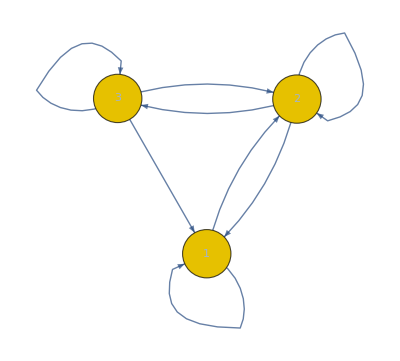
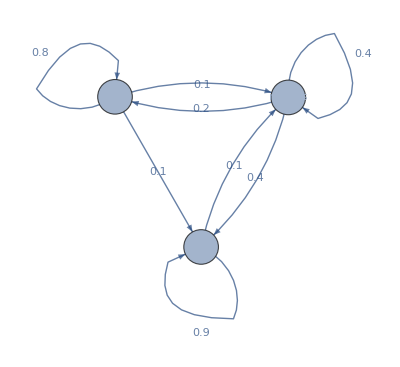
(0.9 | 0.1 | 0
0.4 | 0.4 | 0.2
0.1 | 0.1 | 0.8) | -Graphics- | -Graphics-

```mathematica
Clear["Global`*"]
P={{0.9,0.1,0},{0.4,0.4,0.2},{0.1,0.1,0.8}};
proc=DiscreteMarkovProcess[1,P];
Grid[{{
P//MatrixForm,
Graph[proc],
WeightedAdjacencyGraph[
P/. 0|0.->Infinity,
VertexShapeFunction->"Circle",
VertexSize->0.2,
EdgeLabels->"EdgeWeight",
VertexLabels->(       #[[1]]-> Placed[#[[2]],Center]&/@Transpose[{Range[3],{"poor","mclass","rich"}}]     )
]
}}]
```

#### В городе N каждый из жителей имеет одну из трех профессий A, B, C. Дети отцов, имеющих профессии A, B, C, сохраняют профессии отцов с вероятностями 3/5, 2/3, 1/4 соответственно, а если не сохраняют, то с равными вероятностями выбирают любую из двух профессий. Найти: 1. Распределение по профессиям в следующем поколении, если в данном поколении профессию А имело 20% жителей, B - 30%, C - 50%. 2. Предельное распределение по профессиям

#### Посетитель банка с намерением получить кредит проходит ряд проверок (состояний): е1 - оформление документов; е2 - кредитная история; е3 - возвратность; е4 - платежеспособность. По результатам проверки возможны два исхода: отказ в выдаче кредита (е6) и получение кредита (е5). Одна проверка одна временная единица. Граф этой системы изображен на рис.  Требуется найти среднее количество времени для получения положительного и отрицательного результата Сколько в среднем кредитов одобряются

#### Предприятие имеет автопарк устаревших машин, которые продолжают эксплуатироваться. Целью является получение наибольшей прибыли до полного износа оборудования. При этом, если одна из машин выходит из строя, то общая нагрузка распределяется между оставшимися машинами, что ускоряет их износ. Граф данной системы изображен Требуется: a) Построить матрицу переходных состояний системы; b) Определить среднее время жизни системы, если она в начальный момент времени находилась в состоянии e1 и в состоянии e2 ; c) Найти вектор состояния системы спустя половину времени жизни системы.

## Конечные цепи Маркова: Алгоритм PageRank

### Зададим граф сайта по существующим ссылкам на страницы

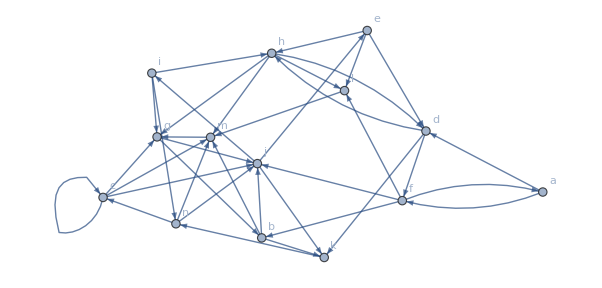

```mathematica
Clear["Global`*"]
edge={a->d,a->f,b->j,b->k,b->m,c->c,c->g,c->j,c->m,d->f,d->h,d->k,e->d,e->h,e->l,f->a,f->b,f->j,f->l,g->b,g->j,h->d,h->g,h->l,h->m,i->g,i->h,i->n,j->e,j->i,j->k,k->n,l->m,m->g,n->c,n->j,n->m};
G=Graph[edge,VertexLabels->"Name"]
```

### Алгоритм на графе PageRankCentrality

```mathematica
prg=PageRankCentrality[G,0.85]
hprg=HighlightGraph[G,VertexList[G],VertexSize->Thread[VertexList[G]->Rescale[prg]]]
sprg=SortBy[Transpose[{VertexList[G], prg}],Last];
%//TableForm
```

{0.0171563,0.0434461,0.0303155,0.0803094,0.141805,0.0859565,0.119438,0.0385367,0.148596,0.051863,0.0508924,0.0425967,0.0508924,0.0981967}

-Graphics-

a | 0.0171563
f | 0.0303155
c | 0.0385367
l | 0.0425967
d | 0.0434461
e | 0.0508924
i | 0.0508924
h | 0.051863
b | 0.0803094
k | 0.0859565
n | 0.0981967
m | 0.119438
j | 0.141805
g | 0.148596

### Алгоритм на графе PageRank на основе цепей Маркова

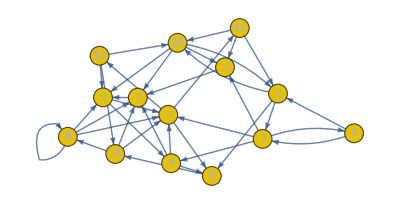

{0.00291071,0.0305625,0.0116429,0.0832646,0.159362,0.0910629,0.119515,0.0483421,0.160708,0.0456012,0.0531205,0.0320179,0.0531205,0.10877}

-Graphics-

a | 0.00291071
f | 0.0116429
d | 0.0305625
l | 0.0320179
h | 0.0456012
c | 0.0483421
i | 0.0531205
e | 0.0531205
b | 0.0832646
k | 0.0910629
n | 0.10877
m | 0.119515
j | 0.159362
g | 0.160708

```mathematica
mt=Normal[AdjacencyMatrix[G]];
mt//MatrixForm;
mat=#/Total[#]&/@ mt;

proc1=DiscreteMarkovProcess[1,mat//N];
MarkovProcessProperties[proc1];
Graph[proc1]
pr=Table[Probability[x==i,x\[Distributed]StationaryDistribution[proc1]],{i,1,14}]

hpr=HighlightGraph[G,VertexList[G],VertexSize->Thread[VertexList[G]->Rescale[pr]]]
spr=SortBy[Transpose[{VertexList[G], pr}],Last];
%//TableForm
```

### Сравнеие PageRankCentrality и PageRank

```mathematica
{{Grid[sprg,Frame->All,Background->{None,{3->Pink}}],Grid[spr,Frame->All,Background->{None,{3->Pink}}]}}//TableForm
```

a | 0.0171563
f | 0.0303155
c | 0.0385367
l | 0.0425967
d | 0.0434461
e | 0.0508924
i | 0.0508924
h | 0.051863
b | 0.0803094
k | 0.0859565
n | 0.0981967
m | 0.119438
j | 0.141805
g | 0.148596 | a | 0.00291071
f | 0.0116429
d | 0.0305625
l | 0.0320179
h | 0.0456012
c | 0.0483421
i | 0.0531205
e | 0.0531205
b | 0.0832646
k | 0.0910629
n | 0.10877
m | 0.119515
j | 0.159362
g | 0.160708

```mathematica
{{hprg,hpr}}//TableForm
```

-Graphics-

#### Секция в машинном цехе состоит из трех станков, с вероятностью 0, 1 ежедневно один из станков может выйти из строя. Станок 1 обеспечивает работу станка 2 и 3, и когда станок 1 выходит из строя, производство в этот день останавливается. Только одни станок может быть восстановлена в тот же день, так что он доступен для работы на следующий день. Если несколько станков выходят из строя, они ремонтируются в приоритетном порядке 1, 2 и 3. Станок после ремонта как предполагается, будет работать на следующий день. Найти вероятность работоспособности производства (долю рабочего времени).

Процесс поломки и ремонта может быть смоделирована как дискретный марковский процесса. 
Перечислим всевозможные комбинации неработающих станков:

```mathematica
failed=Subsets[{1,2,3}]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

Сегодня нет сломанных станков, найдем вероятность того, что один или несколько станков могут сломаться  на следующий день, а могут и  и не сломаться:

```mathematica
transition[i_,j_]/;Length[i]==0:=p^Length[j](1-p)^(3-Length[j])
```

```mathematica
work={};
fail={};
transition[work,fail]
Block[{p=0.1},transition[work,fail]]
```

(1-p)^3

0.729

```mathematica
work={};
fail={1,2,3};
transition[work,fail]
Block[{p=0.1},transition[work,fail]]
```

p^3

0.001

Сегодня сломался один станок, найдем вероятность того, что один станок отремонтируем, а остальные за время ремонта могут сломаться, а и могут и не сломаться (незабываем, что при выходе из строя станка 1  станки 2,  3 прекращают работу):

```mathematica
transition[i_,j_]/;Length[i]==1:=p^Length[j](1-p)^(3-Length[j]-1)Boole[Unequal@@Join[j,i]]
```

```mathematica
work={1};
fail={2};
Join[work,fail]
Unequal@@Join[work,fail]
Boole[Unequal@@Join[work,fail]]
"--------------------------------"
transition[work,fail]
Block[{p=0.1},transition[work,fail]]
```

{1,2}

True

1

--------------------------------

(1-p) p

0.09

Сегодня сломались два станка, найдем вероятность того, что один станок отремонтируем, а остальные за время ремонта могут сломаться, а и могут и не сломаться (незабываем, что при выходе из строя станка 1  станки 2,  3 прекращают работу):

```mathematica
transition[i_,j_]/;Length[i]==2&&Length[j]==1:=(1-p)Boole[Rest[i]==j]
transition[i_,j_]/;Length[i]==2&&Length[j]==2:=p Boole[And@@Thread[First[i]≠j]]
transition[i_,j_]/;Length[i]==2:=0

work={1,3};
fail={2,3};
Block[{p=0.1},transition[work,fail]]
```

0.1

Сегодня сломались три станка, найдем вероятность того, что один станок отремонтируем, а остальные за время ремонта могут сломаться, а и могут и не сломаться (незабываем, что при выходе из строя станка 1  станки 2,  3 прекращают работу):

```mathematica
transition[i_,j_]/;Length[i]==3:=Boole[j=={2,3}]


work={1,2,3};
fail={};
Block[{p=0.1},transition[work,fail]]
```

0

Найдем решение:

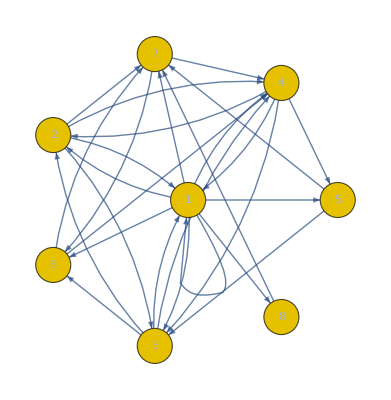

({} | {1} | {2} | {3} | {1,2} | {1,3} | {2,3} | {1,2,3}
0.729 | 0.081 | 0.081 | 0.081 | 0.009 | 0.009 | 0.009 | 0.001
0.81 | 0. | 0.09 | 0.09 | 0. | 0. | 0.01 | 0.
0.81 | 0.09 | 0. | 0.09 | 0. | 0.01 | 0. | 0.
0.81 | 0.09 | 0.09 | 0. | 0.01 | 0. | 0. | 0.
0 | 0. | 0.9 | 0. | 0. | 0. | 0.1 | 0
0 | 0. | 0. | 0.9 | 0. | 0. | 0.1 | 0
0 | 0. | 0. | 0.9 | 0. | 0.1 | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
m=Block[{p=0.1},tab=Table[transition[i,j],{i,failed},{j,failed}]];
P=DiscreteMarkovProcess[1,m];
Graph[P,GraphLayout->"BalloonEmbedding"]
Prepend[tab,failed]//MatrixForm
```

```mathematica
Position[failed,{}|{2}|{3}]
Probability[x==1||x==3||x==4,x\[Distributed]StationaryDistribution[P]]
Probability[x==1,x\[Distributed]StationaryDistribution[P]]
```

{{1},{3},{4}}

0.89947

0.729716

```mathematica
failed[[8]]
FirstPassageTimeDistribution[DiscreteMarkovProcess[8,m],1]//Mean
```

{1,2,3}

```mathematica
3.3593964334705078
```

```mathematica
a={2,3}
b={2,3}
And@@Thread[First[a]≠b]
```

{2,3}

{2,3}

False

```mathematica
transition[{1,3},{2}]
```

0